```mathematica
σx=0.5;
σy=0.25;
f[x_,y_,b_] = (1+b x)Exp[-x^2/σx]Exp[-y^2/σy];
g[x_,σ_,x0_,b_] =  (1+b x)Exp[-(x-x0)^2/σ];
gserie1[x_] =  (1+b x)*(1+(-(x-x0)^2/σ));
gserie2[x_,σ_,x0_,b_] =  (1+b x)*(1+(-(x-x0)^2/σ)+1/2(-(x-x0)^2/σ)^2);
gserie3[x_,σ_,x0_,b_] =  (1+b x)*(1+(-(x-x0)^2/σ)+1/2(-(x-x0)^2/σ)^2+1/6(-(x-x0)^2/σ)^3);
FullSimplify[D[g[x],x]]
FullSimplify[Solve[       D[   D[g[x],x]   ,x ]==0,x]]
FullSimplify[Solve[D[gserie1[x],x]==0,x]]
```

(ⅇ^(-(x-x0)^2/σ) (-2 c (1+b x) (x-x0)+b c σ))/σ

{{x→1/(6 b)(-2+4 b x0+(2^(2/3) (2 (1+b x0)^2+9 b^2 σ))/((-4-4 b x0 (3+b x0 (3+b x0))+3 √6 √(b^2 σ (-4 (1+b x0)^4-18 b^2 (1+b x0)^2 σ-27 b^4 σ^2)))^(1/3))+(-8-8 b x0 (3+b x0 (3+b x0))+6 √6 √(b^2 σ (-4 (1+b x0)^4-18 b^2 (1+b x0)^2 σ-27 b^4 σ^2)))^(1/3))},{x→1/(12 b)(-4+8 b x0+ⅈ (ⅈ+√3) (-8-8 b x0 (3+b x0 (3+b x0))+6 √6 √(b^2 σ (-4 (1+b x0)^4-18 b^2 (1+b x0)^2 σ-27 b^4 σ^2)))^(1/3)+((2 (1+b x0)^2+9 b^2 σ) Root-1.59-2.75 ⅈRoot[-32+#1^3&,2]-1.5874010519681996)/((-4-4 b x0 (3+b x0 (3+b x0))+3 √6 √(b^2 σ (-4 (1+b x0)^4-18 b^2 (1+b x0)^2 σ-27 b^4 σ^2)))^(1/3)))},{x→1/(12 b)(-4+8 b x0+(2 (-2)^(2/3) (2 (1+b x0)^2+9 b^2 σ))/((-4-4 b x0 (3+b x0 (3+b x0))+3 √6 √(b^2 σ (-4 (1+b x0)^4-18 b^2 (1+b x0)^2 σ-27 b^4 σ^2)))^(1/3))-ⅈ (-ⅈ+√3) (-8-8 b x0 (3+b x0 (3+b x0))+6 √6 √(b^2 σ (-4 (1+b x0)^4-18 b^2 (1+b x0)^2 σ-27 b^4 σ^2)))^(1/3))}}

{{x→-(1-2 b x0+√((1+b x0)^2+3 b^2 σ))/(3 b)},{x→(-1+2 b x0+√((1+b x0)^2+3 b^2 σ))/(3 b)}}

-Graphics3D-

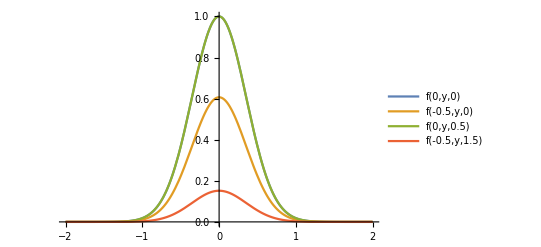

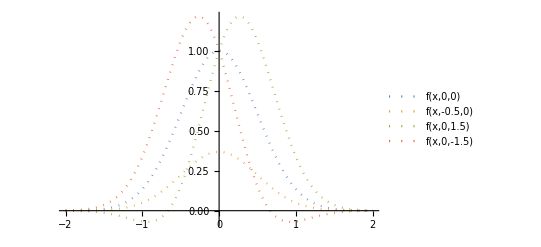

```mathematica
Plot3D[f[x,y,1.5],{x,-1,1},{y,-1,1}]
Plot[{f[0,y,0],f[-0.5,y,0],f[0,y,0.5],f[-0.5,y,1.5]},{y,-2,2},PlotLegends->"Expressions"]
Plot[{f[x,0,0],f[x,-0.5,0],f[x,0,1.5],f[x,0,-1.5]},{x,-2,2},PlotStyle->Dotted,PlotLegends->"Expressions"]
```

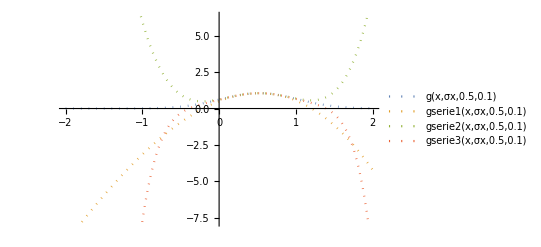

```mathematica
Plot[{g[x,σx,0.5,0.1],gserie1[x,σx,0.5,0.1],gserie2[x,σx,0.5,0.1],gserie3[x,σx,0.5,0.1]},{x,-2,2},PlotStyle->Dotted,PlotLegends->"Expressions"]
```